```mathematica
?Ne*
```

```mathematica
Ne
```

```mathematica
I^2
```

-1

```mathematica
Sin[Pi/2]
```

1

```mathematica
Limit[E^t,t->Infinity]
```

∞

```mathematica
Cos[60 Degree]
```

1/2

```mathematica
23 8
```

184

```mathematica
N[237/4683,50]
```

0.050608584240871236386931454196028187059577194106342

```mathematica
237/4683 //N
```

0.0506086

```mathematica
I^I //N
```

0.20788+0. ⅈ

```mathematica
x=1
```

1

```mathematica
x=.
```

```mathematica
Clear[x]
```

```mathematica
x^2+1
```

1+x^2

```mathematica
%(X^2-1)
```

```mathematica
(1+x^2) (-1+X^2)
```

```mathematica
%%(x^2-1)
```

(-1+x^2) (1+x^2)

```mathematica
%/.{x->y+1}
```

(-1+(1+y)^2) (1+(1+y)^2)

```mathematica
Expand[%]
```

4 y+6 y^2+4 y^3+y^4

```mathematica
Factor[%]
```

y (2+y) (2+2 y+y^2)

```mathematica
{2,3,4}
```

{2,3,4}

```mathematica
{x,y,x+y}
```

{x,y,x+y}

```mathematica
D[%,x]
```

{1,0,1}

```mathematica
t= Table[x^i+y^j,{i,3},{j,2,3}]
```

{{x+y^2,x+y^3},{x^2+y^2,x^2+y^3},{x^3+y^2,x^3+y^3}}

```mathematica
t[[1]]
```

{x+y^2,x+y^3}

```mathematica
%[[2]]
```

x+y^3

```mathematica
TableForm[t]
```

x+y^2 | x+y^3
x^2+y^2 | x^2+y^3
x^3+y^2 | x^3+y^3

```mathematica
t[[1,2]]
```

x+y^3

```mathematica
t[[{1,2}]]
```

{{x+y^2,x+y^3},{x^2+y^2,x^2+y^3}}

```mathematica
Range[3]
```

{1,2,3}

```mathematica
Table[Sin[x y],{x,2},{y,3}]
```

{{Sin[1],Sin[2],Sin[3]},{Sin[2],Sin[4],Sin[6]}}

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
m=DiagonalMatrix[{1,2,3}]
```

{{1,0,0},{0,2,0},{0,0,3}}

```mathematica
Det[m]
```

6

```mathematica
Inverse[m]
```

{{1,0,0},{0,1/2,0},{0,0,1/3}}

```mathematica
%.m
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Eigenvalues[m]
```

{3,2,1}

```mathematica
Eigenvalues[N[m]]
```

{3.,2.,1.}

```mathematica
Eigensystem[m]
```

{{3,2,1},{{0,0,1},{0,1,0},{1,0,0}}}

```mathematica
Limit[Sin[x]/x,x->0]
```

1

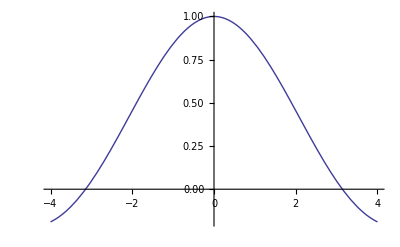

```mathematica
Plot[Sin[x]/x,{x,-4,4}]
```

```mathematica
Limit[Sin[1/x],x->0]
```

Interval[{-1,1}]

```mathematica
D[x^3+4x,x]
```

4+3 x^2

```mathematica
D[x^4-3x^2,{x,3}]
```

24 x

```mathematica
D[Sin[x y]Cos[y],x,y]
```

Cos[y] Cos[x y]-y Cos[x y] Sin[y]-x y Cos[y] Sin[x y]

```mathematica
D[Abs[x],x]
```

Abs'[x]

```mathematica
Limit[(Abs[x]-Abs[0])/x,x->0,Direction->1]
```

-1

```mathematica
Limit[(Abs[x]-Abs[0])/x,x->0,Direction->-1]
```

1

```mathematica
Integrate[x^2+3x+5,x]
```

5 x+(3 x^2)/2+x^3/3

```mathematica
f1=(x+1)/(x^2+3x+5)
```

(1+x)/(5+3 x+x^2)

```mathematica
f2=Integrate[f1,x]
```

-ArcTan[(3+2 x)/(√11)]/(√11)+1/2 Log[5+3 x+x^2]

```mathematica
f3=D[f1,x]
```

-((1+x) (3+2 x))/((5+3 x+x^2)^2)+1/(5+3 x+x^2)

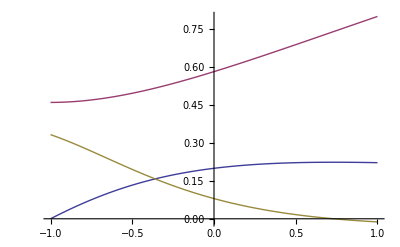

```mathematica
Plot[{f1,f2,f3},{x,-1,1}]
```

```mathematica
NIntegrate[Sin[Sin[x]],{x,0,Pi}]
```

1.78649

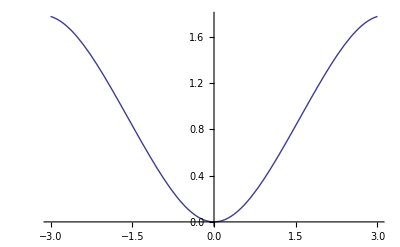

```mathematica
Plot[NIntegrate[Sin[Sin[x]],{x,0,y}],{y,-3,3}]
```

```mathematica
s=Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
f1=Normal[s]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

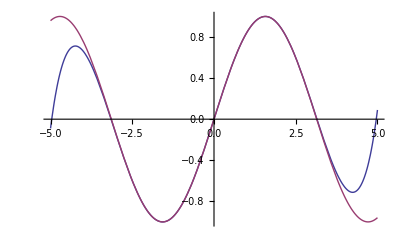

```mathematica
Plot[{f1,Sin[x]},{x,-5,5}]
```

```mathematica
FindMinimum[2Cos[x]+Sin[x],{x,1}]
```

{-2.23607,{x→3.60524}}

```mathematica
NSum[1/n^2,{n,1,Infinity}]
```

1.64493

```mathematica
data=Table[{x,Cos[x]},{x,-2.0,2.0,0.5}]
```

{{-2.,-0.416147},{-1.5,0.0707372},{-1.,0.540302},{-0.5,0.877583},{0.,1.},{0.5,0.877583},{1.,0.540302},{1.5,0.0707372},{2.,-0.416147}}

```mathematica
f=Fit[data,{1,x^2,x^4,x^6,x^8},x]
```

1.-0.499999 x^2+0.0416633 x^4-0.00138442 x^6+0.0000228146 x^8

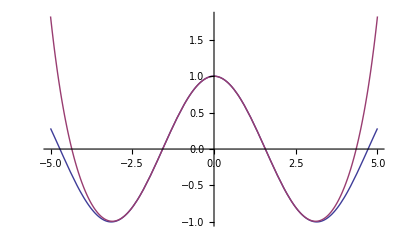

```mathematica
Plot[{Cos[x],f},{x,-5,5}]
```

```mathematica
base={1,x,x^2}
```

{1,x,x^2}

```mathematica
L={{0,0.3},{0.2,0.45},{0.3,0.47},{0.52,0.5},{0.64,0.38},{0.7,0.33},{1.0,0.24}}
```

{{0,0.3},{0.2,0.45},{0.3,0.47},{0.52,0.5},{0.64,0.38},{0.7,0.33},{1.,0.24}}

```mathematica
f=Fit[L,base,x]
```

0.33129+0.596026 x-0.71812 x^2

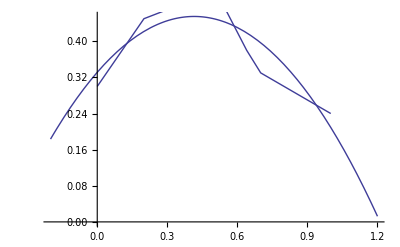

```mathematica
ListPlot[L,PlotJoined->True];
Plot[f,{x,-0.2,1.2}];
Show[%,%%]
```

```mathematica
B=Table[Prime[n],{n,20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
f=Fit[B,{1,x,x^2},x]
```

-1.92368+2.2055 x+0.0746753 x^2

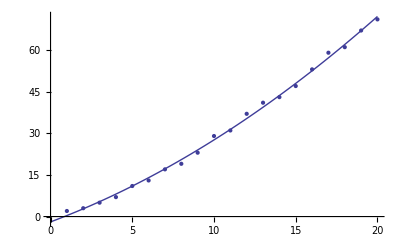

```mathematica
ListPlot[B];
Plot[f,{x,0,20}];
Show[%,%%]
```

```mathematica
x+2y/.{x->1,y->a}
```

1+2 a

```mathematica
x+2y/.{{x->1,y->a},{x->b,y->c}}
```

{1+2 a,b+2 c}

```mathematica
logf[a b c d]/.logf[x_ y_]->logf[x]+logf[y]
```

logf[a]+logf[b c d]

```mathematica
logf[a b c d]//.logf[x_ y_]->logf[x]+logf[y]
```

logf[a]+logf[b]+logf[c]+logf[d]

```mathematica
Clear[f]
```

```mathematica
?f
```

Global`f

```mathematica
f[x_]:=Sin[x]
```

```mathematica
?f
```

Global`f

f[x_]:=Sin[x]

```mathematica
Clear[f]
```

```mathematica
f[n_]:=n f[n-1];f[1]=1
```

1

```mathematica
f[15]
```

1307674368000

```mathematica
15!
```

1307674368000

```mathematica
rd1=Random[]
```

0.107515

```mathematica
rd2:=Random[]
```

```mathematica
{rd1,rd2}
```

{0.107515,0.161224}

```mathematica
{rd1,rd2}
```

{0.107515,0.672541}

```mathematica
Map[#^2&,a+b+c]
```

a^2+b^2+c^2

```mathematica
Map[Function[x,x^2],a+b+c]
```

a^2+b^2+c^2

```mathematica
Plot3D[x^2 Sin[y],{x,-1,1},{y,-Pi,Pi}]
```

-Graphics3D-

```mathematica
Plot3D[x^2 Sin[y],{x,-1,1},{y,-Pi,Pi},PlotPoints->90]
```

-Graphics3D-

```mathematica
Show[%,PlotRange->{0,0.5}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],t/10},{t,0,20Pi},PlotPoints->150]
```

-Graphics3D-

```mathematica
Plot3D[Abs[Gamma[x+I*y]],{x,0.1,3},{y,-3,3}]
```

-Graphics3D-

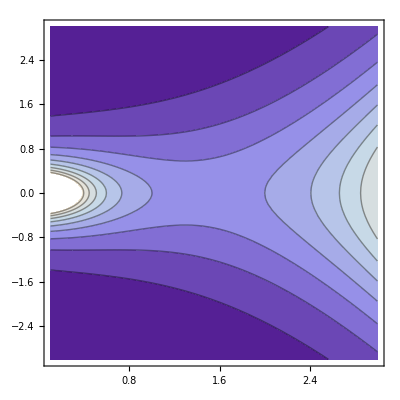

```mathematica
ContourPlot[Abs[Gamma[x+I*y]],{x,0.1,3},{y,-3,3},PlotPoints->30]
```

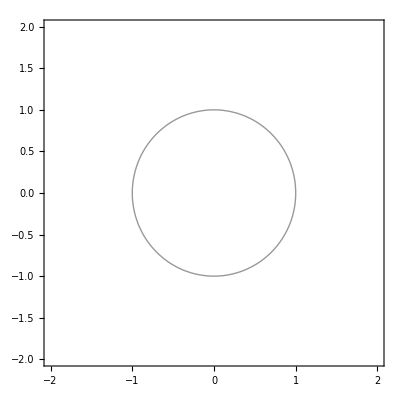

```mathematica
ContourPlot[1-x^2-y^2,{x,-2,2},{y,-2,2},PlotPoints->30,Contours->{0},ContourShading->False]
```